```mathematica
r = 0.1
```

0.1

```mathematica
wp = 0.5
```

0.5

```mathematica
ComplexExpand[1-wp^2/(ⅈ r w+w^2)]
```

1+(ⅈ r w wp^2)/(r^2 w^2+w^4)-(w^2 wp^2)/(r^2 w^2+w^4)

```mathematica
er = 1-(w^2 wp^2)/(r^2 w^2+w^4)
```

1-(0.25 w^2)/(0.01 w^2+w^4)

```mathematica
ei = (r w wp^2)/(r^2 w^2+w^4)
```

(0.025 w)/(0.01 w^2+w^4)

```mathematica
eabs= √(er^2+ei^2)
```

√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)

```mathematica
ni = √((eabs-er)/2)
```

(√(-1+(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)))/(√2)

```mathematica
alpha = w*ni
```

(w √(-1+(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)))/(√2)

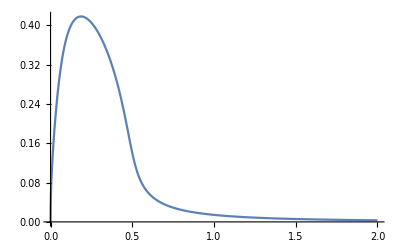

```mathematica
Plot[alpha,{w,0,2}]
```

```mathematica
nr = √((eabs+er)/2)
```

(√(1-(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)))/(√2)

```mathematica
R = ((nr-1)^2+ni^2)/((nr+1)^2+ni^2)
```

(1/2 (-1+(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2))+(-1+(√(1-(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)))/(√2))^2)/(1/2 (-1+(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2))+(1+(√(1-(0.25 w^2)/(0.01 w^2+w^4)+√((0.000625 w^2)/((0.01 w^2+w^4)^2)+(1-(0.25 w^2)/(0.01 w^2+w^4))^2)))/(√2))^2)

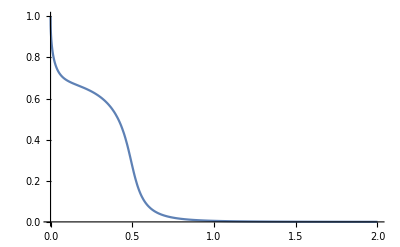

```mathematica
Plot[R,{w,0,2}]
```